```mathematica
sixj[
youngTableau[{{1},{2}}],
youngTableau[{{1,2},{3},{4}}],
youngTableau[{{1},{2}}],
youngTableau[{{1,2},{3}}],
youngTableau[{{1}}],
youngTableau[{{2}}]
]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

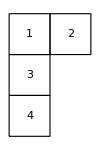
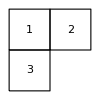
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{youngTableau[{{1},{2}}],
youngTableau[{{1,2},{3},{4}}],
youngTableau[{{1},{2}}],
youngTableau[{{1,2},{3}}],
youngTableau[{{1}}],
youngTableau[{{2}}]}
```

```mathematica
Module[{Ynumbers={{1,2},{3}},Xnumbers={{1},{2}},Znumbers={{1}},repTableau,Zshift,numBoxesX,numBoxesZ,numBoxesY,Xprojector,Zprojector,Yprojector,projector},
repTableau=youngTableau[Ynumbers];
{numBoxesX,numBoxesZ,numBoxesY}=Length[Flatten[#]]&/@{Xnumbers,Znumbers,Ynumbers};
Assert[numBoxesX+numBoxesZ==numBoxesY];
Zshift=shift[Range[numBoxesZ],Range[numBoxesX+1,numBoxesY],repTableau];
Xprojector=youngProjector[youngTableau[{{1},{2}}],repTableau];
Zprojector=youngProjector[youngTableau[{{1}}],repTableau];
Yprojector=youngProjector[youngTableau[{{1,2},{3}}],repTableau];
projector=Yprojector.Zshift.Zprojector.Inverse[Zshift].Xprojector.representation[Cycles[{{2,3}}],repTableau].Yprojector;
(* check Zshift Zshift-inverse or swap *) (* check, should be proportional to Yprojector *)
Yprojector=DeleteCases[Flatten[Yprojector],0];
projector=DeleteCases[Flatten[projector],0];
debug[projector];
debug[Yprojector];
If[Length[projector]==0,debug["is this really meant to vanish?"];Return[0];];
projector[[1]]/Yprojector[[1]]
]
```

debug::msg: Debug: {1/2}

debug::msg: Debug: {1}

1/2

```mathematica
testIdempotency@youngProjector[youngTableau[{{1,2},{3}}],youngTableau[{{1,2},{3}}]]
```

True

```mathematica
testIdempotency@youngProjector[youngTableau[{{1}}],youngTableau[{{1}}]]
```

True

```mathematica
testIdempotency@youngProjector[youngTableau[{{1},{2}}],youngTableau[{{1},{2}}]]
```

True

```mathematica
testRepresentation[3,youngTableau[{{1,2},{3}}]]
```

Success: n = 3 -Graphics-

```mathematica
youngProjector[youngTableau[{{1,2,3},{4,5}}],youngTableau[{{1,2,3},{4,5}}]]//MatrixForm
```

(1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
Module[{f=representation[Cycles[#],youngTableau[{{1,2,3},{4,5}}]]&},1/4*1/6{(f[{{}}]-f[{{2,3}}]-f[{{1,2}}]-f[{{1,3}}]+f[{{1,3,2}}]+f[{{1,2,3}}]),(f[{{}}]+f[{{2,5}}]-f[{{1,4}}]+f[{{1,4},{2,5}}]+f[{{4,5}}]-f[{{2,5,4}}]-f[{{1,4,5}}]+f[{{1,4,2,5}}])}]
```

{{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{1/4,-(1/12),0,0,-(1/6)},{1/8,-(1/12),0,0,-(1/8)},{1/8,-(1/12),1/12,0,-(1/8)},{0,-(1/12),0,1/12,0},{1/12,-(1/12),0,0,0}}}

```mathematica
MatrixForm/@Module[{f=representation[Cycles[#],youngTableau[{{1,2,3},{4,5}}]]&},{f[{{}}],-f[{{2,3}}],-f[{{1,2}}],-f[{{1,3}}],f[{{1,3,2}}],f[{{1,2,3}}]}]
```

{(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1),(-1 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | -1
0 | -1 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0),(-1 | 0 | 0 | 1 | 1
0 | -1 | 0 | 1 | 0
0 | 0 | -1 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1),(-1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | -1 | 0
0 | 0 | 1 | 0 | -1),(1 | -1 | -1 | 0 | 0
0 | -1 | 0 | 1 | 0
0 | 0 | -1 | 0 | 1
0 | -1 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0),(1 | 0 | 0 | -1 | -1
0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | -1
0 | 1 | 0 | -1 | 0
0 | 0 | 1 | 0 | -1)}

```mathematica
youngProjector[youngTableau[{{1},{2},{3}}],youngTableau[{{1,2,3},{4,5}}]]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

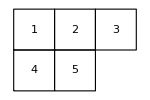
Success: n = 5 -Graphics-

```mathematica
testRepresentation[5,youngTableau[{{1,2,3},{4,5}}]]
```

```mathematica
1/12 Plus@@Module[{f=representation[Cycles[#],youngTableau[{{1,2},{3,4}}]]&},{f[{{}}],-f[{{2,3}}],f[{{3,4}}],-f[{{1,3,4}}],f[{{1,2}}],-f[{{1,2,3}}],f[{{1,2},{3,4}}],-f[{{1,2,3,4}}],-f[{{2,4}}],f[{{1,3},{2,4}}],-f[{{2,4,3}}],f[{{1,3,2,4}}],-f[{{1,4,2}}],f[{{1,4,2,3}}],-f[{{1,4,3,2}}],f[{{1,4},{2,3}}]}]
```

{{11/12,-1/12},{-1/6,1/12}}

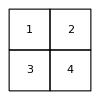
Success: n = 4 -Graphics-

```mathematica
testRepresentation[4,youngTableau[{{1,2},{3,4}}]]
```

Testing (anti)symmetrisers in rep given by

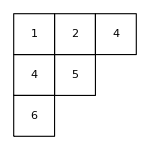

```mathematica
yt=youngTableau[{{1,2,4},{4,5},{6}}]
```

```mathematica
representation[Cycles[{{}}],yt]==#&/@{symmetriser[{1},yt],antisymmetriser[{1},yt]}
```

{True,True}

```mathematica
1/2(representation[Cycles[{{}}],yt]+representation[Cycles[{{1,2}}],yt])==symmetriser[{1,2},yt]
```

True

```mathematica
1/2(representation[Cycles[{{}}],yt]-representation[Cycles[{{1,2}}],yt])==antisymmetriser[{1,2},yt]
```

True

```mathematica
Module[{r=representation[Cycles[#],yt]&},1/6(r[{{}}]+r[{{1,2}}]+r[{{1,3}}]+r[{{2,3}}]+r[{{1,2,3}}]+r[{{1,3,2}}])==symmetriser[{1,2,3},yt]]
```

True

```mathematica
Module[{r=representation[Cycles[#],yt]&},1/6(r[{{}}]-r[{{1,2}}]-r[{{1,3}}]-r[{{2,3}}]+r[{{1,2,3}}]+r[{{1,3,2}}])==antisymmetriser[{1,2,3},yt]]
```

True

```mathematica
Module[{r=representation[Cycles[#],yt]&},1/6(r[{{}}]+r[{{1,2}}]+r[{{1,4}}]+r[{{2,4}}]+r[{{1,2,4}}]+r[{{1,4,2}}])==symmetriser[{1,2,4},yt]]
```

True

```mathematica
Module[{r=representation[Cycles[#],yt]&},1/6(r[{{}}]-r[{{1,2}}]-r[{{1,4}}]-r[{{2,4}}]+r[{{1,2,4}}]+r[{{1,4,2}}])==antisymmetriser[{1,2,4},yt]]
```

True

```mathematica
RandomPermutation[6]
```

Cycles[{{1,3,6,2,4,5}}]

```mathematica
ClearAll[yt]
```

Young Projectors
Use diagram (not tableau) and label [1..n] left to right top to bottom
Get list of indices for rows
Get list of indices for columns
Generate symmetrisers for rows
Generate antisymmetrisers for columns
Young projector is product of symmetriesrs * antisymmetrisers

youngProjector2 :: Young Diagram (labelling projector) -> Young diagram (labelling representation) -> Matrix

```mathematica
youngProjector2[youngDiagram[projectorPartition_],youngDiagram[representationPartition_]]:=Module[{numberOfBoxes=Total[projectorPartition],template=diagramToOrderedTableau[youngDiagram[projectorPartition]],representationTableau=youngTableau[diagramToOrderedTableau[youngDiagram[representationPartition]]],rowIndices,columnIndices,symmetrisers,antisymmetrisers,normalisation},
(*Print[template];*)
rowIndices=reshapeRaggedArray[Range[numberOfBoxes],template];
(*Print[rowIndices];*)
columnIndices=Flatten[rowIndices,{2}];
(*Print[columnIndices];*)
symmetrisers=symmetriser[#,representationTableau]&/@rowIndices;
antisymmetrisers=antisymmetriser[#,representationTableau]&/@columnIndices;
symmetrisers=Dot@@symmetrisers;
antisymmetrisers=Dot@@antisymmetrisers;
normalisation=(1/hookNumber[youngTableau[template]])(Times@@Factorial/@projectorPartition)(Times@@Factorial/@Length/@columnIndices);
(*Print[Length/@rowIndices];
Print[Length/@columnIndices];
Print[normalisation];*)
normalisation*symmetrisers.antisymmetrisers
]
```

```mathematica
youngProjector2[youngDiagram[{3,2,1}],youngDiagram[{3,2,1}]]
```

{{1,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
youngProjector2[youngDiagram[{4,2,1}],youngDiagram[{4,2,1}]]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

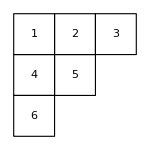
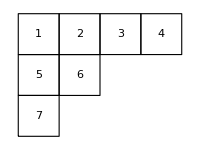

```mathematica
youngTableau[diagramToOrderedTableau[youngDiagram[#]]]&/@{{3,2,1},{4,2,1}}
```

```mathematica
diagramToOrderedTableau[youngDiagram[partition_]]:=Module[{template},
template=Table[Range[partition[[i]]],{i,1,Length[partition]}];
reshapeRaggedArray[Range[Total[partition]],template]
]
```

```mathematica
diagramToOrderedTableau[youngDiagram[{3,2,1}]]
```

{{1,2,3},{4,5},{6}}

```mathematica
youngProjector[youngTableau[{{1,2,3},{4,5},{6}}],youngTableau[{{1,2,3},{4,5},{6}}]]==youngProjector2[youngDiagram[{3,2,1}],youngDiagram[{3,2,1}]]
```

True

```mathematica
youngProjector[youngTableau[{{1,2,3,4},{5,6},{7}}],youngTableau[{{1,2,3,4},{5,6},{7}}]]==youngProjector2[youngDiagram[{4,2,1}],youngDiagram[{4,2,1}]]
```

True

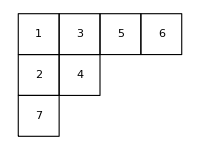
{-Graphics-,-Graphics-}

False

```mathematica
{youngTableau[{{1,3,5,6},{2,4},{7}}],youngTableau[{{1,2,3,4},{5,6},{7}}]}
```